Expected OutPut

{positive,negative,negative,positive,negative,negative,positive,negative,positive,positive,positive,positive,negative,positive,negative,negative,negative,negative,positive,positive,negative,negative,positive,positive,positive,positive,positive,positive,positive,negative,positive,positive,positive,negative,positive,negative,negative,positive,negative,positive,negative,negative,positive,negative,negative,positive,negative,positive,positive,positive,negative,negative,positive,positive,positive,positive,negative,positive,positive,negative,positive,positive,negative,positive,negative,positive,positive,negative,negative,positive,negative,negative,negative,negative,negative,positive,negative,positive,negative,positive,negative,negative,positive,negative,positive,positive,positive,positive,positive,negative,positive,negative,negative,positive,positive,positive,negative,positive,positive,negative,negative,negative,negative,negative,negative,positive,negative,positive,negative,negative,positive,negative,negative,positive,negative,negative,negative,negative,negative,positive,negative,positive,negative,positive,negative,positive,negative,negative,positive,negative,negative,positive,positive,positive,positive,negative,negative,positive,negative,positive,negative,negative,negative,negative,negative,negative,negative,positive,negative,positive,negative,negative,negative,negative,negative,negative,positive,negative,positive,positive,negative,negative,positive,positive,positive,positive,negative,negative,negative,negative,negative,positive,negative,positive,negative,positive,positive,negative,negative,negative,positive,positive,negative,negative,negative,negative,negative,negative,negative,negative,positive,positive,positive,negative,positive,positive,positive,positive,positive}

RandomForst OutPut

{positive,positive,negative,positive,negative,negative,positive,negative,positive,positive,positive,positive,negative,negative,negative,negative,positive,positive,positive,negative,positive,negative,negative,negative,positive,positive,negative,positive,positive,negative,negative,positive,positive,positive,positive,negative,negative,negative,positive,negative,negative,positive,negative,positive,negative,positive,negative,negative,positive,negative,negative,negative,negative,negative,negative,positive,negative,negative,negative,positive,negative,positive,negative,positive,negative,positive,positive,negative,negative,negative,negative,negative,positive,positive,negative,positive,negative,negative,positive,positive,negative,negative,positive,negative,positive,negative,negative,positive,positive,negative,negative,positive,positive,positive,negative,negative,positive,positive,negative,positive,negative,positive,positive,positive,negative,positive,negative,positive,negative,negative,positive,negative,negative,positive,negative,positive,negative,negative,positive,negative,negative,negative,positive,positive,negative,negative,positive,negative,positive,negative,positive,negative,negative,negative,positive,negative,negative,positive,positive,negative,negative,negative,negative,negative,positive,negative,positive,positive,positive,negative,positive,negative,negative,negative,positive,negative,positive,negative,negative,negative,negative,negative,positive,positive,positive,positive,negative,positive,positive,positive,positive,negative,negative,negative,positive,positive,positive,negative,negative,negative,positive,negative,negative,positive,negative,negative,negative,negative,negative,positive,negative,positive,positive,negative,positive,negative,positive,positive,positive}

NeuralNetwork OutPut

{positive,positive,positive,positive,positive,positive,positive,positive,positive,positive,negative,positive,negative,positive,negative,negative,positive,positive,positive,positive,negative,positive,positive,negative,positive,positive,negative,positive,positive,negative,negative,negative,positive,positive,negative,positive,positive,positive,negative,negative,negative,positive,negative,negative,negative,positive,positive,negative,positive,positive,negative,negative,positive,positive,negative,positive,negative,negative,positive,positive,positive,negative,negative,positive,negative,positive,negative,negative,negative,negative,negative,positive,positive,positive,negative,positive,negative,negative,negative,positive,positive,negative,positive,negative,positive,positive,positive,negative,positive,negative,negative,positive,positive,positive,negative,positive,positive,negative,positive,positive,positive,positive,negative,negative,negative,positive,negative,positive,positive,negative,positive,negative,negative,positive,negative,positive,positive,negative,positive,negative,negative,positive,negative,positive,negative,positive,positive,negative,positive,negative,positive,positive,negative,positive,negative,positive,negative,negative,positive,positive,negative,negative,negative,negative,positive,negative,positive,positive,positive,negative,positive,negative,positive,positive,negative,negative,negative,negative,positive,negative,negative,negative,positive,positive,positive,positive,positive,negative,positive,positive,negative,positive,negative,positive,positive,positive,positive,negative,negative,negative,positive,negative,positive,negative,positive,positive,negative,negative,negative,positive,negative,positive,positive,negative,positive,positive,positive,positive,positive}

SVM OutPut

{positive,positive,negative,positive,positive,negative,negative,positive,positive,positive,negative,positive,negative,negative,positive,negative,positive,positive,positive,positive,positive,negative,positive,negative,positive,positive,negative,positive,positive,negative,negative,positive,positive,negative,negative,positive,negative,positive,positive,negative,positive,positive,negative,positive,negative,negative,positive,positive,positive,negative,positive,negative,positive,positive,positive,positive,negative,positive,positive,positive,positive,positive,negative,negative,negative,positive,negative,negative,negative,negative,negative,positive,positive,positive,negative,positive,negative,negative,negative,positive,positive,negative,positive,negative,positive,positive,positive,positive,positive,negative,positive,positive,positive,positive,negative,positive,positive,positive,positive,positive,negative,negative,negative,negative,negative,positive,negative,positive,negative,negative,positive,positive,negative,positive,positive,negative,positive,negative,positive,negative,negative,positive,negative,positive,negative,negative,positive,negative,positive,negative,positive,positive,positive,positive,positive,negative,negative,negative,positive,positive,negative,negative,negative,negative,positive,negative,positive,positive,positive,negative,positive,negative,positive,positive,negative,negative,positive,positive,positive,negative,negative,negative,positive,positive,positive,positive,negative,positive,negative,positive,negative,positive,positive,positive,negative,positive,positive,negative,positive,negative,positive,positive,negative,positive,negative,positive,negative,positive,negative,positive,negative,positive,positive,positive,positive,negative,negative,positive,positive}

0.613065

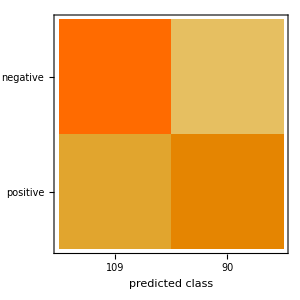

0.628141

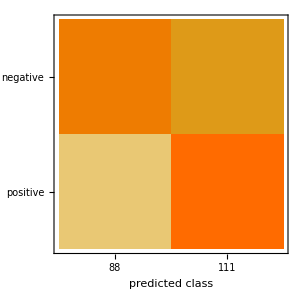

0.648241

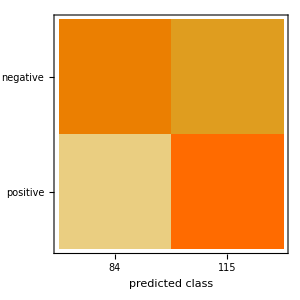

Precision for Random Forest, Neural Networks, SVM

<|negative→0.633028,positive→0.588889|>

<|negative→0.681818,positive→0.585586|>

<|negative→0.714286,positive→0.6|>

Recall for Random Forest, Neural Networks, SVM

<|negative→0.650943,positive→0.569892|>

<|negative→0.566038,positive→0.698925|>

<|negative→0.566038,positive→0.741935|>

ROC Curve for Random Forest, Neural Networks, SVM

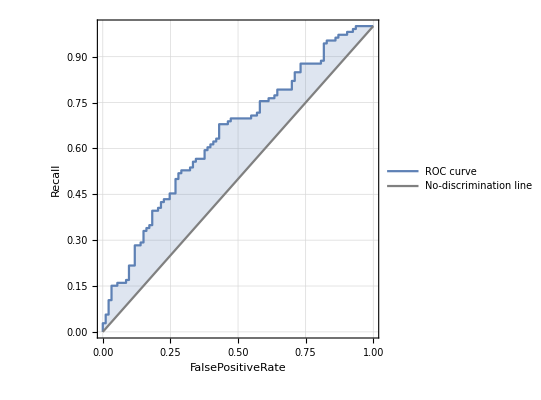
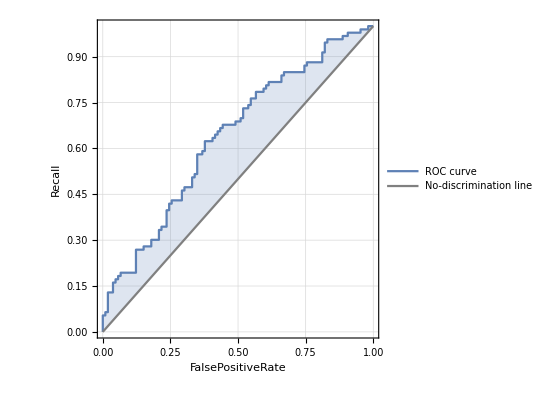
<|negative→-Graphics-,positive→-Graphics-|>

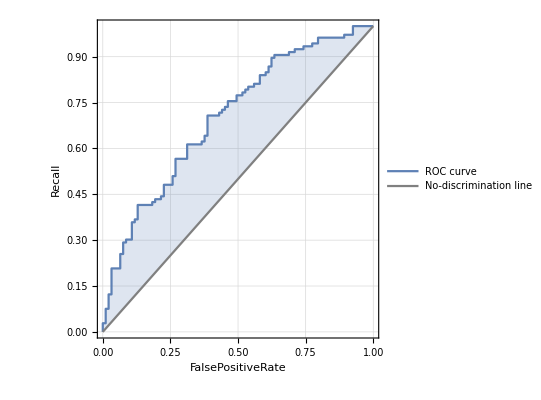
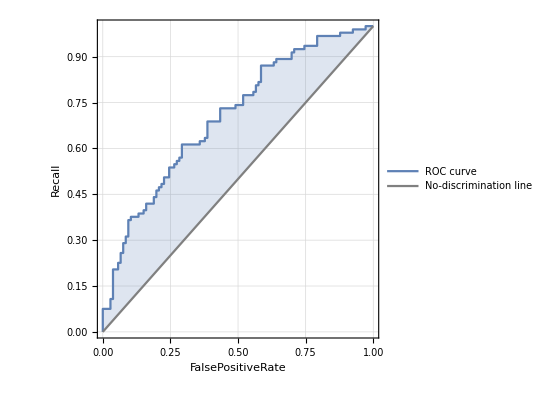
<|negative→-Graphics-,positive→-Graphics-|>

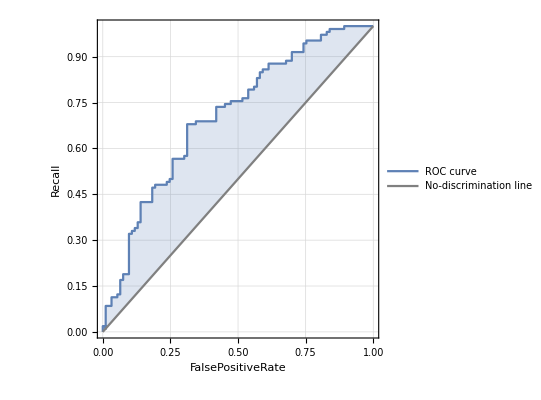
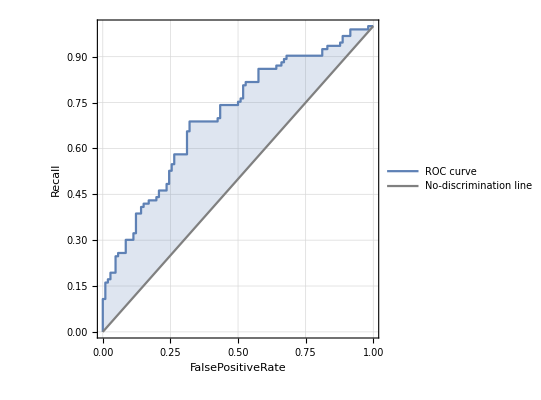
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
rawData=OpenRead["reviews.csv"];
punctuation=Alternatives@@Characters[",.?:;\"!-"];
reviews=Map[StringSplit[#,"|"]&,StringReplace[ReadList[rawData,String,1000],punctuation->""]];
testDt=Drop[Take[reviews,{1,-1,5}],1];
train=Drop[reviews,{1,-1,5}];
(*PreProcessing the Data*)
trainData=ToLowerCase[DeleteDuplicates[train]];
testData=ToLowerCase[DeleteDuplicates[testDt]];
adjTrainData=Flatten[TextCases[trainData[[All,2]],"Adjective"]];
adjTestTrainData=Flatten[TextCases[testData[[All,2]],"Adjective"]];
negativeWords={"aren't","cannot","can't","couldn't","didn't","doesn't","don't","hadn't","hasn't","have-not","have-nots","haven't","isn't","mustn't","neither","no","nor","not","shan't","shouldn't","wasn't","weren't","won't","wouldn't"};
negtaiveRules=Thread[negativeWords->#]&/@{"not"};
list=Complement[DictionaryLookup["*"],DeleteStopwords[DictionaryLookup["*"]]];
list1=ToLowerCase[Complement[list,negativeWords]];
adjNotlist=Union[adjTrainData,{"not"}];
list2=Complement[ToLowerCase[DictionaryLookup["*"]],adjNotlist];
train3=ReplaceAll[negtaiveRules[[1]]][TextWords[trainData[[All,2]]]];
test3=ReplaceAll[negtaiveRules[[1]]][TextWords[testData[[All,2]]]];
testlen=Length[test3]+1;
testDataMain={{"empty"}};
testsamp;
(*Removing unwanted text Like Stop Words and checking whether word is Valid*)
For[i=1,i<testlen,i++,
Clear[testsamp];
testsamp=DeleteDuplicates[Select[test3[[i,All]],!MemberQ[list1,#]& ]];
wordsLen=Length[testsamp]+1;
For[j=1,j<wordsLen,j++,
isValid=DictionaryWordQ[testsamp[[j]]];
If[!isValid,wordsLen=Length[testsamp];
testsamp=Delete[testsamp,j];,testsamp]];
AppendTo[testDataMain,testsamp];];
finalTestData=Drop[testDataMain,1];
(*Removing unwanted text Like Stop Words and checking whether word is Valid on Train Data*)
len=Length[train3]+1;
samp;
trainDataMain={{"empty"}};
For[i=1,i<len,i++,
Clear[samp];
samp=DeleteDuplicates[Select[train3[[i,All]],MemberQ[adjNotlist,#]∧ !MemberQ[list1,#]& ]];
wordsLen=Length[samp]+1;
For[j=1,j<wordsLen,j++,
isValid=DictionaryWordQ[samp[[j]]];
If[!isValid,
wordsLen=Length[samp];
samp=Delete[samp,j];,samp
]];
AppendTo[trainDataMain,samp];]
finalTrainData=Drop[trainDataMain,1];
finalRedTrainData=finalTrainData[[All]];
trainingset=Flatten[MapThread[{#1->#2}&,{finalRedTrainData,trainData[[All,1]]}]];
Print["Expected OutPut"];
testData[[All,1]]
testDatat=finalTestData[[All]];
(*Performing Feature Extraction*)
fe=FeatureExtraction[finalRedTrainData,"TFIDF"];
(*Applying the classify Methods*)
rfclassifier=Classify[finalRedTrainData->trainData[[All,1]],FeatureExtractor->fe,Method->{"RandomForest"}];
Print["RandomForst OutPut"];
rfclassifier[testDatat]
neuralclassifier=Classify[finalRedTrainData->trainData[[All,1]],FeatureExtractor->fe,Method->{"NeuralNetwork"}];
Print["NeuralNetwork OutPut"];
neuralclassifier[testDatat]
svmclassifier=Classify[finalRedTrainData->trainData[[All,1]],FeatureExtractor->fe,Method->"SupportVectorMachine"];
Print["SVM OutPut"];
svmclassifier[testDatat]

(*Performance Analysis*)
ClassifierMeasurements[rfclassifier,testDatat[[All]]-> testData[[All,1]],"Accuracy"]
ClassifierMeasurements[rfclassifier,testDatat[[All]]-> testData[[All,1]],"ConfusionMatrixPlot"]

ClassifierMeasurements[neuralclassifier,testDatat[[All]]-> testData[[All,1]],"Accuracy"]
ClassifierMeasurements[neuralclassifier,testDatat[[All]]-> testData[[All,1]],"ConfusionMatrixPlot"]

ClassifierMeasurements[svmclassifier,testDatat[[All]]-> testData[[All,1]],"Accuracy"]
ClassifierMeasurements[svmclassifier,testDatat[[All]]-> testData[[All,1]],"ConfusionMatrixPlot"]

Print["Precision for Random Forest, Neural Networks, SVM"]
ClassifierMeasurements[rfclassifier,testDatat[[All]]-> testData[[All,1]],"Precision"]
ClassifierMeasurements[neuralclassifier,testDatat[[All]]-> testData[[All,1]],"Precision"]
ClassifierMeasurements[svmclassifier,testDatat[[All]]-> testData[[All,1]],"Precision"]

Print["Recall for Random Forest, Neural Networks, SVM"]
ClassifierMeasurements[rfclassifier,testDatat[[All]]-> testData[[All,1]],"Recall"]
ClassifierMeasurements[neuralclassifier,testDatat[[All]]-> testData[[All,1]],"Recall"]
ClassifierMeasurements[svmclassifier,testDatat[[All]]-> testData[[All,1]],"Recall"]

Print["ROC Curve for Random Forest, Neural Networks, SVM"]
ClassifierMeasurements[rfclassifier,testDatat[[All]]-> testData[[All,1]],"ROCCurve"]
ClassifierMeasurements[neuralclassifier,testDatat[[All]]-> testData[[All,1]],"ROCCurve"]
ClassifierMeasurements[svmclassifier,testDatat[[All]]-> testData[[All,1]],"ROCCurve"]
```